```mathematica
trans:=(r - r a  Exp[I ϕ1])/(1-r^2   a  Exp[I ϕ1])
```

```mathematica
n:=3.45;
R1:=10 10^(-6);
d:= 2 Pi R1
λ:=1550 10^(-9); (* resonant wavelrngth *)
Q1:=1×10^5;
h := 1(* 0 for passive 1 for active*)
g := 140.85154393399725
α:=(2 Pi n)/(λ  Q1)
a:= Exp[-(α -g) d/2]
t:=√(1-r^2)
r:= 0.985
```

```mathematica
α
```

139.852

```mathematica
a
```

1.00003

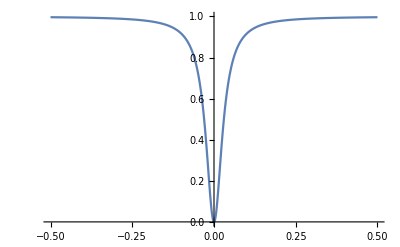

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
transdata:=Table[{ϕ1,Abs[trans]^2},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->{0,1}]
```

```mathematica
ϕ := Pi + ϕ1  + 2ArcTan[(r a  Sin[ϕ1])/(r-r a Cos[ϕ1])]
```

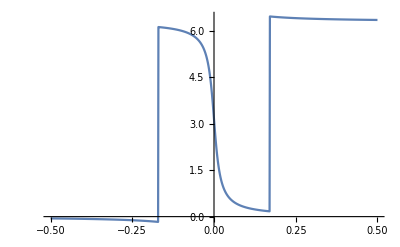

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
phasedata:=Table[{ϕ1,ϕ},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[phasedata,PlotRange->All]
```

```mathematica
r - a
```

-0.0297156